```mathematica
plot=Plot3D[WxyA,{xt,-1500,2000},{yt,-2000,1200},PlotRange->Full,LabelStyle->Directive[FontFamily->"Times New Roman",16],PlotTheme->Classic,PlotStyle->Opacity[0.9],Mesh->30]
```

-Graphics3D-

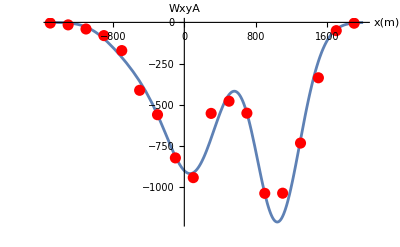

```mathematica
Plot[WxyA/. yt->0,{xt,-1500,2000},Epilog->{Red,PointSize[0.02],Point[{{-1500,-4},{-1300,-15},{-1100,-40},{-900,-80},{-700,-171},{-500,-411.9},{-300,-560},{-100,-822},{100,-941.62},{300,-552},{500,-478},{700,-550.5},{900,-1037},{1100,-1036},{1300,-732},{1500,-336},{1700,-50},{1900,-5}}]},PlotRange->All,AxesLabel->{"x(m)","Wxy(mm)"}]
```

```mathematica
plot=Plot3D[WxyA,{xt,-1500,2000},{yt,-2000,0},PlotRange->Full,LabelStyle->Directive[FontFamily->"Times New Roman",16],PlotTheme->Classic,Mesh->30];
points={{-1500,0,-4},{-1300,0,-15},{-1100,0,-40},{-900,0,-80},{-700,0,-171},{-500,0,-411.9},{-300,0,-560},{-100,0,-822},{100,0,-941.62},{300,0,-552},{500,0,-478},{700,0,-550.5},{900,0,-1037},{1100,0,-1036},{1300,0,-732},{1500,0,-336},{1700,0,-50},{1900,0,-5}}
Show[plot,Graphics3D[{Red,PointSize[0.02],Point[points]}]]
```

{{-1500,0,-4},{-1300,0,-15},{-1100,0,-40},{-900,0,-80},{-700,0,-171},{-500,0,-411.9},{-300,0,-560},{-100,0,-822},{100,0,-941.62},{300,0,-552},{500,0,-478},{700,0,-550.5},{900,0,-1037},{1100,0,-1036},{1300,0,-732},{1500,0,-336},{1700,0,-50},{1900,0,-5}}

-Graphics3D-

```mathematica
|
```